```mathematica
(*Mathematica*)
```

```mathematica
Clear[s,w]
```

```mathematica
(*First so(5)*)
s[1]={{0,1,0,0,0},
           {1,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[2]={{0,0,1,0,0},
           {0,0,0,0,0},
          {1,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[3]={{0,0,0,1,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0},
{0,0,0,0,0}};
s[4]={{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0}};
s[5]={{0,0,0,0,0},
{0,0,1,0,0},
{0,1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[10]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,1},
        { 0,0,0,1,0}};
s[9]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,1,0,0}};
s[8]={{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,1,0,0,0}};
s[7]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,1,0},
{0,0,1,0,0},
{0,0,0,0,0}};
s[6]={{0,0,0,0,0},
{0,0,0,1,0},
{0,0,0,0,0},
{0,1,0,0,0},
{0,0,0,0,0}};
(* second so(5) *)
s[11]={{0,I,0,0,0},
           {-I,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[12]={{0,0,-I,0,0},
           {0,0,0,0,0},
          {I,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[13]={{0,0,0,I,0},
{0,0,0,0,0},
{0,0,0,0,0},
{-I,0,0,0,0},
{0,0,0,0,0}};
s[14]={{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{I,0,0,0,0}};
s[15]={{0,0,0,0,0},
{0,0,I,0,0},
{0,-I,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[20]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,I},
        { 0,0,0,-I,0}};
s[19]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,I,0,0}};
s[18]={{0,0,0,0,0},
{0,0,0,0,I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,-I,0,0,0}};
s[17]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,I,0},
{0,0,-I,0,0},
{0,0,0,0,0}};
s[16]={{0,0,0,0,0},
{0,0,0,-I,0},
{0,0,0,0,0},
{0,I,0,0,0},
{0,0,0,0,0}};
(* DIAGONAL four: n-1 matrices*)
(* zero trace with normalization Sqrt[n*(n-1)/2]*)
s[21]={{1,0,0,0,0},
{0,-1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[22]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,-2,0,0},
{0,0,0,0,0},
{0,0,0,0,-1}}/Sqrt[7/2];
s[23]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,-3,0},
{0,0,0,0,0}}/Sqrt[6];
s[24]={{2,0,0,0,0},
{0,2,0,0,0},
{0,0,2,0,0},
{0,0,0,-3,0},
{0,0,0,0,-3}}/Sqrt[15];
s[25]=IdentityMatrix[5]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
(*U(1)*SU(5):anti-deSitter groupm sum*)
```

```mathematica
gs=N[Sum[s[i],{i,25}]]
```

{{3.45917,1.+1. ⅈ,1.-1. ⅈ,1.+1. ⅈ,1.-1. ⅈ},{1.-1. ⅈ,1.45917,1.+1. ⅈ,1.-1. ⅈ,1.+1. ⅈ},{1.+1. ⅈ,1.-1. ⅈ,0.855601,1.+1. ⅈ,1.-1. ⅈ},{1.-1. ⅈ,1.+1. ⅈ,1.-1. ⅈ,-0.999342,1.+1. ⅈ},{1.+1. ⅈ,1.-1. ⅈ,1.+1. ⅈ,1.-1. ⅈ,-0.309119}}

```mathematica
(*trace normalized to 10*)
```

```mathematica
ca0=gs.Transpose[gs]/(15.921311363729505/10)//Chop
```

{{7.51562,6.85769-1.25618 ⅈ,3.96624+1.63527 ⅈ,2.80117-2.80034 ⅈ,5.74705+2.36682 ⅈ},{6.85769-1.25618 ⅈ,1.33731,5.22242-0.379094 ⅈ,1.54499+1.54416 ⅈ,1.97851-1.11064 ⅈ},{3.96624+1.63527 ⅈ,5.22242-0.379094 ⅈ,0.459795,3.67825-1.16507 ⅈ,1.59942+0.731548 ⅈ},{2.80117-2.80034 ⅈ,1.54499+1.54416 ⅈ,3.67825-1.16507 ⅈ,0.627262,2.9467+0.433521 ⅈ},{5.74705+2.36682 ⅈ,1.97851-1.11064 ⅈ,1.59942+0.731548 ⅈ,2.9467+0.433521 ⅈ,0.0600168}}

```mathematica
TableForm[ca0]
```

7.51562 | 6.85769-1.25618 ⅈ | 3.96624+1.63527 ⅈ | 2.80117-2.80034 ⅈ | 5.74705+2.36682 ⅈ
6.85769-1.25618 ⅈ | 1.33731 | 5.22242-0.379094 ⅈ | 1.54499+1.54416 ⅈ | 1.97851-1.11064 ⅈ
3.96624+1.63527 ⅈ | 5.22242-0.379094 ⅈ | 0.459795 | 3.67825-1.16507 ⅈ | 1.59942+0.731548 ⅈ
2.80117-2.80034 ⅈ | 1.54499+1.54416 ⅈ | 3.67825-1.16507 ⅈ | 0.627262 | 2.9467+0.433521 ⅈ
5.74705+2.36682 ⅈ | 1.97851-1.11064 ⅈ | 1.59942+0.731548 ⅈ | 2.9467+0.433521 ⅈ | 0.0600168

```mathematica
Det[ca0]//Chop
```

45.3116

```mathematica
Tr[ca0]
```

10.

```mathematica
ei=Eigenvalues[ca0]//Chop
```

{18.0521,-4.06779-3.39372 ⅈ,-4.06779+3.39372 ⅈ,0.0417536+0.296135 ⅈ,0.0417536-0.296135 ⅈ}

```mathematica
Abs[ei]
```

{18.0521,5.29757,5.29757,0.299064,0.299064}

```mathematica
pl=Apply[Plus,ei]//Chop
```

10.

```mathematica
pl-Det[ca0]/10//Chop
```

5.46884

```mathematica
ga=ComplexListPlot[ei,PlotStyle->Red,ImageSize->Full];
```

```mathematica
Apply[Plus,ei]//Chop
```

10.

```mathematica
p[x_]=CharacteristicPolynomial[ca0,x]//Chop
```

45.3116-31.681 x+497.585 x^2+117.883 x^3+10. x^4-x^5

```mathematica
(*rotate 72 degrees*)
```

```mathematica
r=N[Exp[2*Pi*I/5]]
```

0.309017+0.951057 ⅈ

```mathematica
rc=-Conjugate[r]
```

-0.309017+0.951057 ⅈ

```mathematica
ca0c=Table[If[i>j,ca0[[i,j]]*r,If[j>i,ca0[[i,j]]*rc,If[i==j,ca0[[i,j]],Nothing]]],{i,5},{j,5}]
```

{{7.51562,-0.924446+6.91023 ⅈ,-2.78087+3.26679 ⅈ,1.79767+3.52942 ⅈ,-4.02691+4.73438 ⅈ},{3.31384+6.13387 ⅈ,1.33731,-1.25328+5.08396 ⅈ,-1.94601+0.9922 ⅈ,0.44489+2.22488 ⅈ},{-0.329601+4.27744 ⅈ,1.97435+4.84967 ⅈ,0.459795,-0.0285959+3.85825 ⅈ,-1.18999+1.29508 ⅈ},{3.52889+1.79872 ⅈ,-0.991158+1.94655 ⅈ,2.24469+3.1382 ⅈ,0.627262,-1.32288+2.66852 ⅈ},{-0.475045+6.19715 ⅈ,1.66768+1.53847 ⅈ,-0.201496+1.7472 ⅈ,0.498279+2.93645 ⅈ,0.0600168}}

```mathematica
Det[ca0c]//Chop
```

-604.732-2206.13 ⅈ

```mathematica
Tr[ca0c]
```

10.

```mathematica
eic=Eigenvalues[ca0c]//Chop
```

{2.64168+14.1793 ⅈ,6.94033-6.6676 ⅈ,-2.24719-5.6005 ⅈ,1.79537-2.27415 ⅈ,0.869808+0.362946 ⅈ}

```mathematica
Apply[Plus,eic]//Chop
```

10.

```mathematica
Apply[Plus,Abs[eic]]//Chop
```

33.9219

```mathematica
gb=ComplexListPlot[eic,PlotStyle->Blue];
```

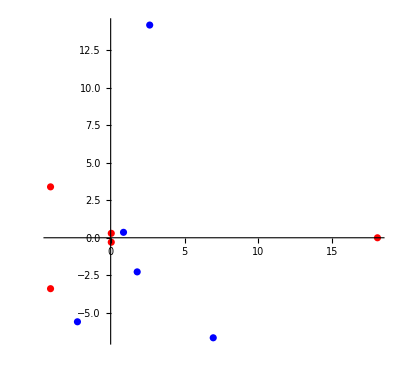

```mathematica
Show[{ga,gb},PlotRange->All]
```

```mathematica
q[x_]=CharacteristicPolynomial[ca0c,x]//Chop
```

(-604.732-2206.13 ⅈ)+(693.195+2701.25 ⅈ) x+(594.045-1046.55 ⅈ) x^2-159.001 x^3+10. x^4-x^5

```mathematica
ph[x_]=x^2*q[x]/p[x]
```

(x^2 ((-604.732-2206.13 ⅈ)+(693.195+2701.25 ⅈ) x+(594.045-1046.55 ⅈ) x^2-159.001 x^3+10. x^4-x^5))/(45.3116-31.681 x+497.585 x^2+117.883 x^3+10. x^4-x^5)

```mathematica
g1=JuliaSetPlot[ph[x]/N[3],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False];
```

```mathematica
g2=ListPlot[JuliaSetPoints[ph[x]/N[3],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_Cartan_SU5_antidesitter_Hermanrings_scale3_both.jpg",{g1,g2}]
```

Julia_Cartan_SU5_antidesitter_Hermanrings_scale3_both.jpg

```mathematica
(*end*)
```